# QFT compilation

## Toy device

Connectivity

```mathematica
qubitsnum=3;
```

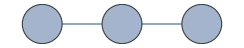

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

```mathematica
Options[ToyDevice]={
qubitsNum->3,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->10,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.995,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{0,1},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.995,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{0,1},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Compilation : QFT

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=ToyDevice[StdPassiveNoise->False,EFSingle->{0,0},EFTwo->{0,0}];
```

```mathematica
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,3];
```

```mathematica
conf["ansatzspace"]={0,1,2};
conf["fixansatz"]={Subscript[Rx, 0][θ],Subscript[Rz, 0][θ],Subscript[C, 0][Subscript[Rz, 1][θ]],Subscript[Rz, 0][θ],Subscript[C, 0][Subscript[Rz, 1][θ]],Subscript[Rz, 1][θ]};
conf["grad"]="NG";
conf["αtikhonov"]=10^-5;
```

Compilation with a fixed ansatz

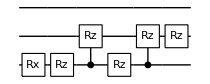
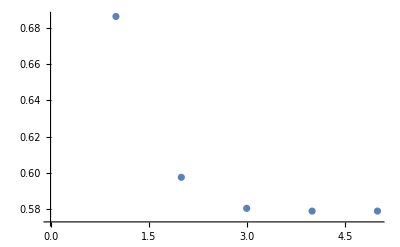
0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

Compilation with a fixed ansatz

0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

Compilation with a fixed ansatz

0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

Compilation with a fixed ansatz

0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

Compilation with a fixed ansatz

0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

Compilation with a fixed ansatz

0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

Compilation with a fixed ansatz

0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

Compilation with a fixed ansatz

0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

Compilation with a fixed ansatz

0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

Compilation with a fixed ansatz

0.57894
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.15319,θ_2→0.859191,θ_3→0.958224,θ_4→0.859191,θ_5→0.958224,θ_6→1.80301|>
-Graphics-

{{0.125266,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.122941,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.120711,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.120569,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.120264,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.119584,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.119895,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.12101,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.118698,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.120777,{Null,Null,Null,Null,Null,Null,Null,Null}}}

```mathematica
Table[Timing@CircuitSynthesis[3,conf],{10}]
```

Compilation with a fixed ansatz

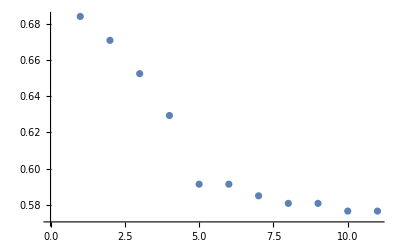
0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

Compilation with a fixed ansatz

0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

Compilation with a fixed ansatz

0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

Compilation with a fixed ansatz

0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

Compilation with a fixed ansatz

0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

Compilation with a fixed ansatz

0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

Compilation with a fixed ansatz

0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

Compilation with a fixed ansatz

0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

Compilation with a fixed ansatz

0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

Compilation with a fixed ansatz

0.576498
-Graphics-
{Rx_0[θ_1],Rz_0[θ_2],C_0[Rz_1[θ_3]],Rz_0[θ_4],C_0[Rz_1[θ_5]],Rz_1[θ_6]}
<|θ_1→1.17147,θ_2→-1.15768,θ_3→-5.39098,θ_4→2.96698,θ_5→7.43774,θ_6→2.10085|>
-Graphics-

{{0.31465,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.311812,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.310724,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.306012,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.31564,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.318283,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.338194,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.320332,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.31845,{Null,Null,Null,Null,Null,Null,Null,Null}},{0.306664,{Null,Null,Null,Null,Null,Null,Null,Null}}}

```mathematica
Table[Timing@CircuitSynthesis[3,conf],{10}]
```